```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/uqbrob14/xsection

```mathematica
tab=Import["testdata_mat.txt","Table"];
```

```mathematica
Evalues = tab[[5]];
qvalues = tab[[8]];
Kvalues=tab[[11;;]];
```

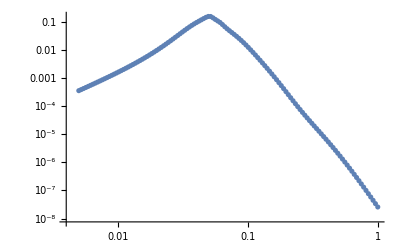

```mathematica
ListLogLogPlot[Transpose[{qvalues,Kvalues[[5]]}]]
```